```mathematica
Λ = 75 10^-9; (*Unit: meter*)
ωp = 6.18;      (* unit: eV *)
γ = 20 10^-3; (* unit: eV *)
ϵ[ω_] := 1 - ωp^2/(ω (ω + I γ));
α[ω_] := (ϵ[ω]-1)/(ϵ[ω]+2)  ; (* unit: 4 Subscript[πϵ, 0] a^3 *)
a = 25 10^-9; (*Unit: meter*)
ω0 = 2.63;  (* c/Λ, unit: eV*)
```

```mathematica
ωxy[k_] := ωp N[√(1/3(1 + (a/Λ)^3)Re[PolyLog[3, ⅇ^(ⅈ k)] + PolyLog[3, ⅇ^(-ⅈ k)]])]; (*unit of k: 1 / Λ, output unit: eV*)
```

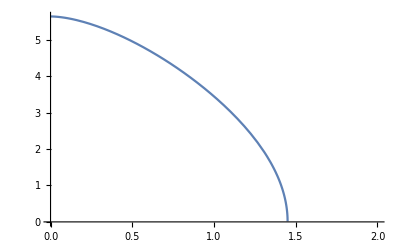

```mathematica
Plot[ωxy[k], {k, 0, 2}]
```

```mathematica
ωz[k_] := ωp N[√(1/3(1 -2 (a/Λ)^3)Re[PolyLog[3, ⅇ^(ⅈ k)] + PolyLog[3, ⅇ^(-ⅈ k)]])]; (*unit of k: 1 / Λ, output unit: eV*)
```

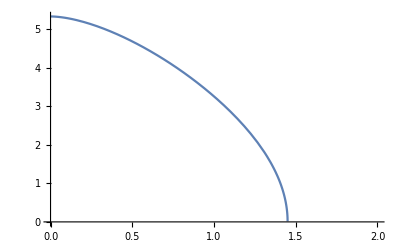

```mathematica
Plot[ωz[k], {k, 0, 2}]
```

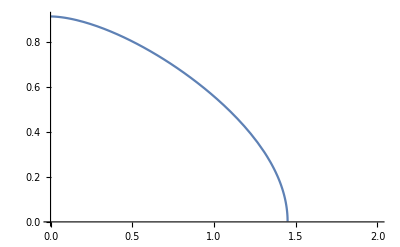
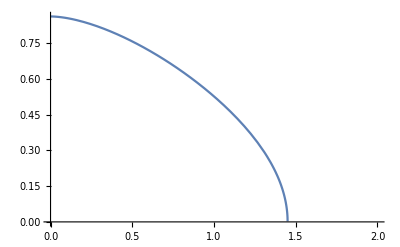
```mathematica
Show[-Graphics-, -Graphics-]
```

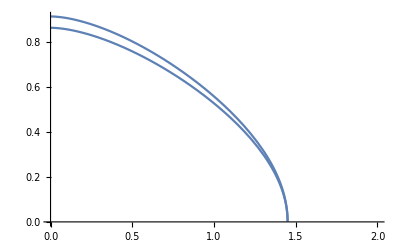

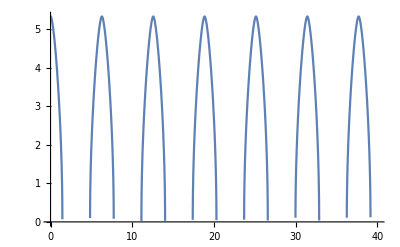

```mathematica
Plot[ωz[k], {k, 0, 40}]
```

```mathematica
αxy[ω_, k_] := N[1/(1/α[ω]-(ω/ω0)^3 (a/Λ)^3(ω0/ω(PolyLog[1, ⅇ^(ⅈ (ω/ω0-k))]+PolyLog[1, ⅇ^(ⅈ (ω/ω0+k))]) + ⅈ(ω0/ω)^2(PolyLog[2, ⅇ^(ⅈ (ω/ω0-k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+k))]) - (ω0/ω)^3(PolyLog[3, ⅇ^(ⅈ (ω/ω0-k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+k))]) ))];
 (*unit: ω eV, k  1/Λ*)
```

```mathematica
Im[αxy[5.63381, 1]]
```

0.0534185

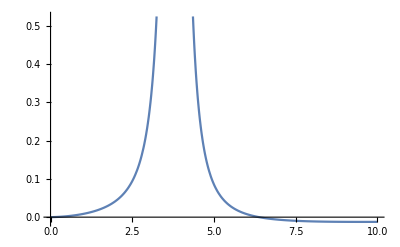

```mathematica
Plot[Im[αxy[ω, 0.0]], {ω, 0, 10}]
```